# Integrals For Dummies

## If we can, you can!

Progetto d’esame: Matematica Computazionale & Calcolo Numerico e Software Didattico.
A.A 2017 - 2018

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

-Graphics- -Graphics- -Graphics- -Graphics-

Autori:

Tommaso Saracchini  | Domenico Coriale | Giuseppe De Palma | Eduart Uzeir

Per iniziare ad usare questa applicazione ed imparare tutto ciò che serve sugli integrali, devi premere il pulsante START. Buon divertimento!

```mathematica
Button[-Graphics-,SetDirectory[NotebookDirectory[]]; EvaluationNotebook[]; ButtonData->NotebookLocate["Prolog"];]
```

-Graphics-

# Scegli Cosa Vuoi Fare:

```mathematica
Framed[Grid[{{Button[-Graphics-, ButtonData-> NotebookLocate["Index"]; ], "          ", Button[-Graphics-, 
nbAllenamento = NotebookOpen["Allenamento.nb"];]}}],  FrameStyle->Directive[Orange, 52], RoundingRadius->10, Alignment->Baseline]
```

-Graphics- |            | -Graphics-

# Indice

## Primo Livello:

```mathematica
Print[Framed[Button[Style["Integrali Definiti" ,FontSize->Large, FontColor->Blue], NotebookLocate["DefiniteTheory"], Appearance->"Frameless" ],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Integrali Definiti

```mathematica
Print[Framed[Button[Style["Integrali Indefiniti", FontColor->Blue, FontSize->Large],NotebookLocate["IndefiniteTheory"], Appearance->"Frameless"],FrameStyle->Directive[Orange,12],Background->LightBlue]]
```

Integrali Indefiniti

## Secondo Livello:

```mathematica
Print[Framed[Button[Style["Teorema Fondamentale", FontColor->Blue, FontSize->Large],NotebookLocate["TeoremaFondamentale"], Appearance->"Frameless"],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Teorema Fondamentale

```mathematica
Print[Framed[Button[Style["Metodi di Risoluzione degli Integrali", FontSize->Large, FontColor->Blue], NotebookLocate["Metodi"], Appearance->"Frameless"],FrameStyle->Directive[Orange,12], Background->LightBlue]]
```

Metodi di Risoluzione degli Integrali

## Allenamento:

```mathematica
Button[-Graphics-, nbAllenamento = NotebookOpen["Allenamento.nb"];]
```

-Graphics-

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

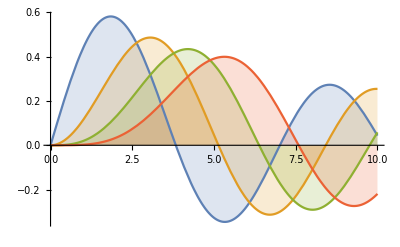

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

# Integrali Definiti

```mathematica
"Ascoltami: " Audio[File["Audio/s4.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

Che cosa sono gli integrali definiti? E soprattutto: a cosa servono?
In Matematica, così come in tutte le discipline scientifiche, può capitare di dover calcolare l’area sottostante ad una curva descritta da una funzione: gli integrali ci permettono di fare proprio questo.
Prendiamo una funzione f(x), come ad esempio quella nell’immagine di sotto, e due punti a e b sull’asse delle x che sono gli estremi dell’intervallo al quale siamo interessati.
Ci chiediamo: come facciamo a calcolare l’area tra la curva , l’asse delle ‘x’ e i due segmenti verticali x=a e x=b?
Per farlo ci servono gli integrali!

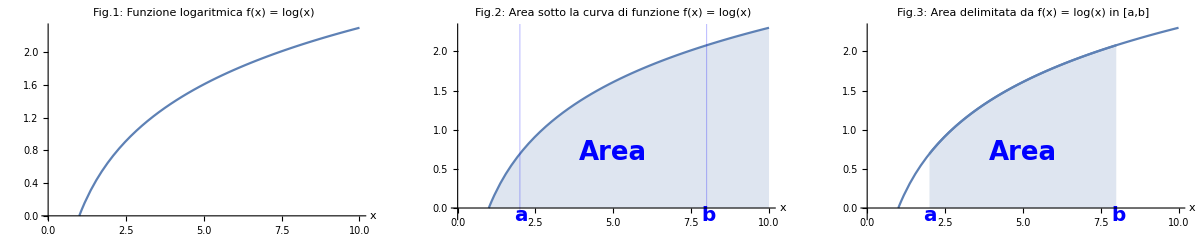

```mathematica
<<"Grafici.m";
grafico1
```

```mathematica
Framed[Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

## Andiamo per passi: Area del rettangolo

```mathematica
"Ascoltami: " Audio[File["Audio/s5.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

Prendiamo una funzione semplice (la funzione costante), cioè una retta parallela all’asse delle ‘x’ (ad esempio la retta di equazione f(x) = 4).
Siamo interessati a calcolare l’area sotto la funzione, nell’intervallo di estremi a = 1 e b = 3, come in figura. 
Come facciamo?

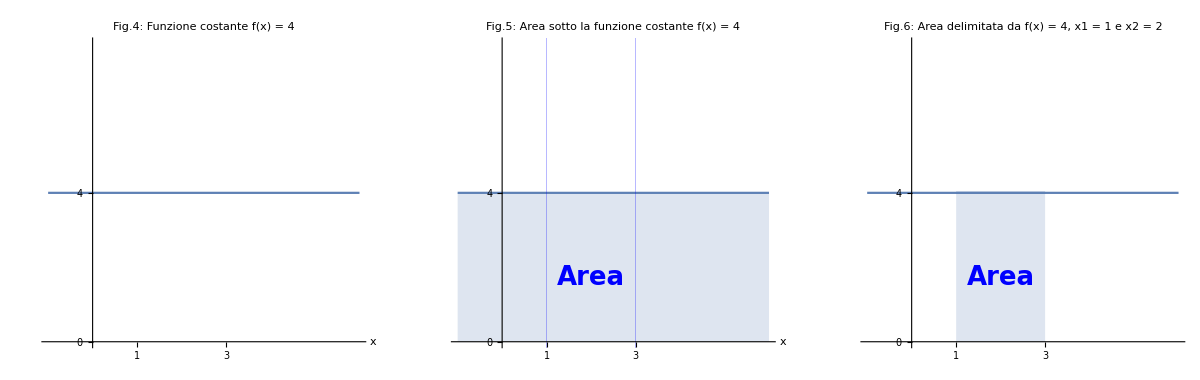

```mathematica
<<"Grafici.m";
grafico2
```

Semplice : è un rettangolo!!! Sapendo che il rettangolo dato ha base (B) uguale a 2 ed altezza (H) uguale a 4, l'area sarà 8. [A(rettangolo) = B x H]
Quindi diciamo che l'integrale da 1 a 3 della funzione f (x) = 4 in dx è uguale a 8! Facile no?! 

In simboli

```mathematica
<<MaTeX`
MaTeX[HoldForm[A=Integrate[f[x],{x,a,b}] = Integrate[4, {x, 1, 3}]= 8], Magnification->3]
```

-Graphics-

Ti stai chiedendo cosè dx? Lo scopriamo tra poco...! Intanto facciamo un altro semplice esempio.

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[RETTANGOLO, "http://www.youmath.it/formulari/formulari-di-geometria-piana/337-tutte-le-formule-sul-rettangolo.html"]]]
```

Approfondimenti:  [RETTANGOLO](http://www.youmath.it/formulari/formulari-di-geometria-piana/337-tutte-le-formule-sul-rettangolo.html)

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["DefiniteTheory"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Andiamo per passi: Area del trapezio

```mathematica
"Ascoltami: " Audio[File["Audio/s6.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

Prendiamo come funzione una qualunque retta inclinata, ad esempio f(x) = x. 
Come facciamo a calcolare l’area nell’intervallo di estremi a = 1 e b = 5?

Questa volta abbiamo di fronte un trapezio!
Conoscendo la formula per calcolare l’area del trapezio [ A(trapezio) =  ((B(minore) + B(maggiore)) x H)/2= ((1 + 5)x 4)/2 = 12 ] arriviamo a dire che:

```mathematica
<<MaTeX`
MaTeX[HoldForm[A = Integrate[f[x], {x, a,b}] = Integrate[(x), {x, 1, 5}]=12], Magnification->3]
```

-Graphics-

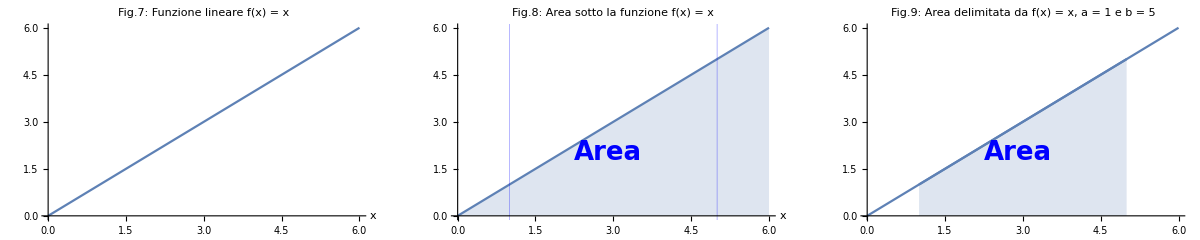

```mathematica
<<"Grafici.m";
grafico3
```

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[TRAPEZIO, "http://www.youmath.it/formulari/formulari-di-geometria-piana/405-tutte-le-formule-sul-trapezio-qualsiasi-rettangolo-isoscele.html"]]]
```

Approfondimenti:  [TRAPEZIO](http://www.youmath.it/formulari/formulari-di-geometria-piana/405-tutte-le-formule-sul-trapezio-qualsiasi-rettangolo-isoscele.html)

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Andiamo per passi: Area delle Curve

Ma se volessimo calcolare l’area sotto delle funzioni curve, come questa per esempio:

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x]=e^x], Magnification->3]
```

-Graphics-

Oppure

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x] = x^3 - 8x^2 + 100], Magnification->3]
```

-Graphics-

In questo caso la geometria euclidea non puo’ aiutarci... per fortuna ci sono gli integrali definiti.

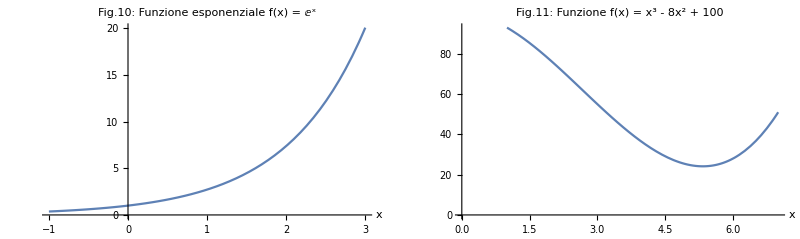

```mathematica
<<"Grafici.m";
grafico4
```

```mathematica
<<MaTeX`
Style[Grid[{{"Abbiamo incontrato nelle slide precedenti la scrittura",MaTeX[HoldForm[Integrate[f[x], {x,a,b}]], Magnification->3],", ma cosa vogliamo dire con questi simboli?"}}],FontFamily->"Nimbus Sans L", FontSize->26]
```

Abbiamo incontrato nelle slide precedenti la scrittura | -Graphics- | , ma cosa vogliamo dire con questi simboli?

⟶  ∫  sta per “somma” di cosa? Lo vedremo tra poco;

⟶ a e b sono gli estremi dell’intervallo di integrazione, cioè la “base” dell’area che vogliamo calcolare;

⟶ f(x) è la funzione che conosciamo;

⟶ dx rappresenta anche lui una “base”, ma quale base?

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite2"];]Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite4"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

```mathematica
"Ascoltami: " Audio[File["Audio/s8.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

Possiamo pensare di dividere l’intervallo [a, b] in 4 intervalli uguali. Tracciamo dei segmenti verticali in modo da costruire dei rettangoli che non oltrepassano la funzione, come in figura.

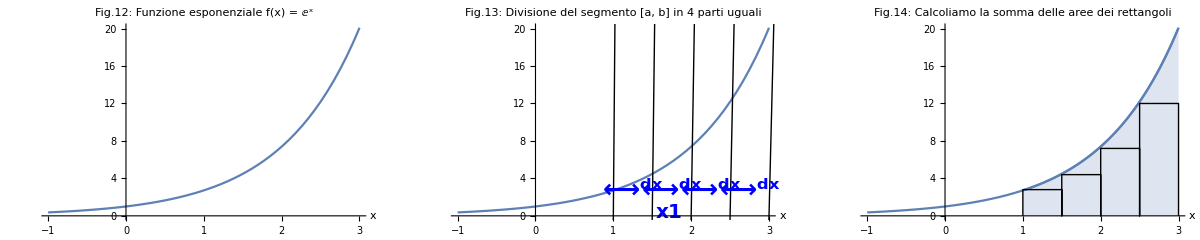

```mathematica
<<"Grafici.m";
grafico5
```

Abbiamo quindi quattro rettangoli con la stessa base dx, ognuno con altezza diversa, ad esempio il primo ha altezza f(a), il secondo f(x1) e cosi via ... fino all’ultimo f(x3).
Chiamo S4 la somma delle aree dei quattro rettangoli che ne sono usciti.
Osserviamo che se sommiamo le aree di questi 4 rettangoli otteniamo un’area minore dell’area A sottesa alla curva (indicata con il color blu in figura 14) , 
cioè abbiamo che S4 < A. 
Possiamo fare meglio?!

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite3"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite5"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

```mathematica
"Ascoltami: " Audio[File["Audio/s9.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

Come possiamo ridurre l’errore tra la misura dell’area che abbiamo calcolato e la misura dell’area “vera”?
Possiamo dividere ulteriormente l’intervallo! Ad esempio in 10 intervalli uguali.

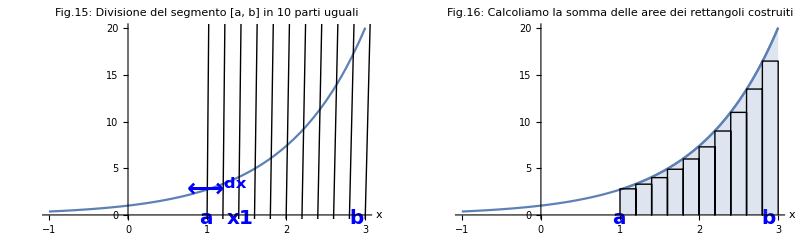

```mathematica
<<"Grafici.m";
grafico6
```

Abbiamo però lo stesso problema, possiamo notare dalla figura che la somma dell’area nei 10 rettangoli, cioè S10 è ancora minore dell’area A sottesa alla curva.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite4"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Definite6"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

```mathematica
"Ascoltami: " Audio[File["Audio/s10.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Definiti"]
```

Ascoltami:

In generale se dividessimo l’intervallo [a, b] in N intervalli avremmo che la somma SN delle aree degli N rettangoli, sarà sempre minore dell’area che vogliamo calcolare, 
cioè SN < A per ogni N numero di intervalli.
Prendiamo per esempio la funzione in figura:

```mathematica
<<MaTeX`
MaTeX[HoldForm[f[x] = e ^x], Magnification->3]
```

-Graphics-

Muovi il cursore e osserva che, al crescere di N, i rettangoli diventano sempre più piccoli e la differenza tra SN e A è sempre minore.

```mathematica
f[x_]:= ⅇ^x
plotChart[nrettangoli_] := Module[{}, low = 0; high = 2;
delta = (high - low)/nrettangoli;
colsum = Graphics[{FaceForm[{Opacity[0.7]}], Table[{Hue[1, 0.6, 0.8], EdgeForm[Thin], Rectangle[{low + n * delta, 0}, {low + (n + 1) * delta, f[low + n * delta]}]}, {n, 1, nrettangoli}]}, ImageSize->500, AspectRatio->1];
curve=Plot[f[x], {x, low, high}, PlotStyle->Thick, ImageSize->60];];
Manipulate[plotChart[nrettangoli];
Show[{colsum, curve}], {{nrettangoli,4}, 2, 80}]
```

Show::gcomb: Could not combine the graphics objects in Show[{colsum,curve}].

```mathematica
<<MaTeX`
Style[Grid[{{"Non ci resta altro da fare che \"mandare N all'infinito\", e cioè calcolare", MaTeX["\\lim_{N ->\\infty}S_N", Magnification->3], "."}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Non ci resta altro da fare che "mandare N all'infinito", e cioè calcolare | -Graphics- | .

Il risultato che ne salterà fuori sarà proprio l'area che stavamo cercando!

	    Quindi, ricapitoliamo: l'area che vogliamo calcolare è

```mathematica
<<MaTeX`
MaTeX["A=\\int_{a}^{b} f(x)\,dx", Magnification->3]
```

-Graphics-

ovvero, 
⟶ la somma ∫
⟶ nell’intervallo [a, b] di rettangoli
⟶ di base dx
⟶ e altezza f(x)

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[LIMITI, "http://www.youmath.it/lezioni/analisi-matematica/limiti-continuita-e-asintoti.html"]]]
```

Approfondimenti:  [LIMITI](http://www.youmath.it/lezioni/analisi-matematica/limiti-continuita-e-asintoti.html)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Integrali Indefiniti!", {"Project.nb","IndefiniteTheory"}],FrameStyle->Directive[Orange,12],Background->LightBlue]
```

Passa alla prossima sezione:  Integrali Indefiniti!Project.nbIndefiniteTheoryProject.nb

```mathematica
Framed[
Button[ 
ImageRotate[-Graphics-],ButtonData->NotebookLocate["Definite5"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Integrali Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s11.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Indefiniti"]
```

Ascoltami:

Prima di spiegare che cosa è l’integrale indefinito, dobbiamo fare qualche premessa.
Partiamo dalla definizione di primitiva di una funzione: 
Sia f : [a, b]→ℝ, una funzione continua. Una funzione F(x) derivabile nell’intervallo (a, b) è una primitiva (o antiderivata) della funzione f se:

```mathematica
<<MaTeX`
Style[Grid[{{MaTeX["F'(x) = f(x)", Magnification->3], "per ogni",MaTeX["x \\in (a,b)", Magnification->3]}}], FontFamily->"Nimbus Sans L", Italic, FontSize->28]
```

-Graphics- | per ogni | -Graphics-

In altre parole una primitiva di una funzione f(x) non è altro che una funzione che una volta derivata da proprio f(x).

## Esempi

Calcolo delle primitive di alcune funzioni semplici

```mathematica
<<"Grafici.m";
tabViewInt
```

12345678910

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[DERIVATE, "http://www.youmath.it/lezioni/analisi-matematica/derivate.html"]]]
```

Approfondimenti:  [DERIVATE](http://www.youmath.it/lezioni/analisi-matematica/derivate.html)

```mathematica
Framed[
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Indefinite1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

## Ancora primitive...

```mathematica
"Ascoltami: " Audio[File["Audio/s12.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Indfiniti"]
```

Ascoltami:

Possiamo fare un osservazione:
Avete notato che nella definizione c’è scritto “una primitiva” e non “la primitiva”?

```mathematica
<<MaTeX`
Style[Grid[{{"Riprendendo, ad esempio, una delle funzioni nella slide precedente:", MaTeX["f(x) = 2x", Magnification->3]}}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

Riprendendo, ad esempio, una delle funzioni nella slide precedente: | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{"Possiamo osservare che", MaTeX["F(x) = x^2 + 1", Magnification->3], "è anch'essa una primitiva di",MaTeX["f(x)", Magnification->3],  "infatti", MaTeX[ "(x^2 + 1)' = 2x", Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Possiamo osservare che | -Graphics- | è anch'essa una primitiva di | -Graphics- | infatti | -Graphics-

Abbiamo trovato due primitive di una stessa funzione! Ma quante ce ne saranno?

Basti pensare che, tornando all'esempio precedente, potevamo aggiungere alla primitiva F(x) una costante qualsiasi dato che la derivata di una costante vale zero.
Infatti possiamo scrivere:

```mathematica
<<MaTeX`
MaTeX["(x^2 + C)' = (x^2)' + C' = 2x", Magnification->3]
```

-Graphics-

Perciò vediamo che se una funzione f(x) ammette primitiva F(x), allora ne ha  infinite che differiscono tutte da F(x) di una costante additiva ( C ).

A questo punto sapendo che se una funzione ammette una primitiva, ne ammette infinite, ha quindi senso definire l'insieme 
di tutte le primitive di una funzione e di attribuirgli un nome: 

lo chiameremo integrale indefinito di una funzione.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["IndefiniteTheory"];]
Button[-Graphics-, ButtonData->NotebookLocate["Index"];] Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Indefinite2"]; ], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Definizione

```mathematica
"Ascoltami: " Audio[File["Audio/s13.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Indefiniti"]
```

Ascoltami:

Sia f(x) una funzione, si chiama integrale indefinito di f(x) l’insieme di tutte le primitive della funzione f(x) e si indica con il simbolo:

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[f[x], x]], Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{"In base a quanto detto sulle primitive possiamo dire che:", 
MaTeX[HoldForm[Integrate[f[x], x]=F[x] + C], Magnification->3], "dove",
 MaTeX["F(x)", Magnification->3], "è una primitiva di", MaTeX["f(x)", Magnification->3]}}], FontSize->26, FontFamily->"Nimbus Sans L"]
```

In base a quanto detto sulle primitive possiamo dire che: | -Graphics- | dove | -Graphics- | è una primitiva di | -Graphics-

## Nota bene!

Anche se la notazione non lo lascia intendere esplicitamente sottolineiamo che l’integrale indefinito identifica un insieme di funzioni
e non una funzione in particolare.
Questo fatto viene messo in evidenza dalla costante additiva C, che è arbitraria e non deve essere omessa.
Facciamo qualche semplice esempio per chiarire le idee:

```mathematica
<<MaTeX`
Style[Grid[{
{"1.", MaTeX[HoldForm[Integrate[x,x] = x^2/2 + C], Magnification->3], "          2.", MaTeX[HoldForm[Integrate[e^x,x] = e^x + C], Magnification->3] },
{"3.", MaTeX[HoldForm[Integrate[1/x, x] = Log[|x|] + C], Magnification->3], "          4.", 
MaTeX[HoldForm[Integrate[1/x^2, x] = -1/x + C], Magnification->3] },
{"5.", MaTeX[HoldForm[Integrate[x^2,x] = x^3/3 + C], Magnification->3]}
}], FontFamily->"Nimbus Sans L", FontSize->28, Italic]
```

1. | -Graphics- |           2. | -Graphics-
3. | -Graphics- |           4. | -Graphics-
5. | -Graphics- |  |

per C costante qualsiasi.

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["il Teorema Fondamentale!", {"Project.nb","TeoremaFondamentale"}],FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  il Teorema Fondamentale!Project.nbTeoremaFondamentaleProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Indefinite1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Teorema Fondamentale

```mathematica
"Ascoltami: " Audio[File["Audio/s14.mp3"], Appearance->"Minimal", AudioLabel->"Teorema Fondamentale"]
```

Ascoltami:

Quello che vediamo ora è che la notazione utilizzata per gli integrali definiti e indefiniti è molto simile... perchè?
 
Le definizioni che abbiamo dato ad entrambe sono completamente diverse.
L’integrale definito di una funzione in un certo intervallo indica un’area e cioè un numero.
L’integrale indefinito di una funzione è invece un insieme di funzioni, che non ha nulla a che vedere con il concetto di area.
Ma allora perchè le loro notazioni sono cosi simili? La risposta la troviamo nel seguente teorema.

## Teorema fondamentale del calcolo integrale

Sia f:[a, b]→ℝ una funzione e sia G(x) una sua primitiva. Allora:

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[f[x], {x,a,b}] = G[b] - G[a]], Magnification->3]
```

-Graphics-

Questo teorema fondamentale stabilisce un legame tra l'integrale definito e l'integrale indefinito, il quale non era per niente ovvio dalle sole definizioni date ad entrambi!

In particolare, ci permette di risolvere integrali definiti usando il concetto di primitiva di una funzione, e cioè con gli integrali indefiniti.
Ecco svelato il perchè delle notazioni molto simili, ma andiamo subito a calcolare il nostro primo integrale.

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[TEOREMA FONDAMENTALE DEL CALCOLO INTEGRALE, 
"http://www.youmath.it/lezioni/analisi-matematica/integrali/653-teorema-fondamentale-del-calcolo-integrale.html"]]]
```

Approfondimenti:  [CALCOLO DEL FONDAMENTALE INTEGRALE TEOREMA](http://www.youmath.it/lezioni/analisi-matematica/integrali/653-teorema-fondamentale-del-calcolo-integrale.html)

```mathematica
Framed[
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Teorema1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

## Il mio primo integrale ■□

```mathematica
"Ascoltami: " Audio[File["Audio/s15.mp3"], Appearance->"Minimal", AudioLabel->"Il mio primo Integrale"]
```

Ascoltami:

Vogliamo calcolare l’area sottesa alla curva di funzione f(x)=x^2 nell’intervallo [1, 2]

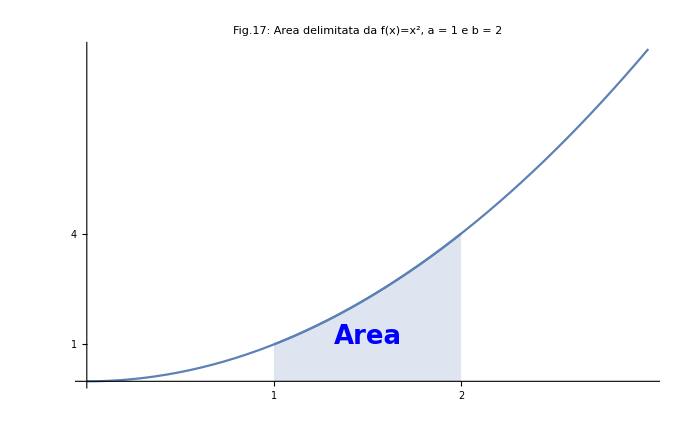

```mathematica
<<"Grafici.m";
grafico7
```

```mathematica
<<MaTeX`
Style[Grid[{{ "Quindi possiamo calcolare l'area A con la seguente formula:", MaTeX[HoldForm[A = Integrate[x^2, {x, 1, 2}]], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Quindi possiamo calcolare l'area A con la seguente formula: | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{ "Il teorema precedente mi dice che devo trovare una primitiva della funzione", MaTeX[HoldForm[f[x] = x^2], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Il teorema precedente mi dice che devo trovare una primitiva della funzione | -Graphics-

```mathematica
<<MaTeX`
Style[Grid[{{ "Ricordandosi le regole di derivazione dei polinomi, non dovrebbe risultare difficile trovare:", MaTeX[HoldForm[G[x] = x^3/3+C], Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Ricordandosi le regole di derivazione dei polinomi, non dovrebbe risultare difficile trovare: | -Graphics-

Trucco:
Notate che, mi basta conoscere una sola primitiva di f(x), e quindi per semplicità posso prendere la primitiva con la costante C = 0!
Una volta trovata G(x) vado ad applicare il teorema:

```mathematica
<<MaTeX`
MaTeX[HoldForm[A =Integrate[x^2, {x,1,2}] = G[2] - G[1] = 2^3/3 - 1^3/3 = 8/3 - 1/3 = 7/3], Magnification->3]
```

-Graphics-

Osservate che se avessimo preso una qualunque altra primitiva G(x) = x^3/3 + C, con C un numero qualsiasi, avremmo avuto lo stesso risultato.

```mathematica
<<MaTeX`
MaTeX[HoldForm[A =Integrate[x^2, {x,1,2}] = G[2] - G[1] = (2^3/3 + C) - (1^3/3 + C) = 8/3 + C - 1/3 -C = 7/3], Magnification->3]
```

-Graphics-

Questo perche, in questo procedimento, le costanti si eliminano a vicenda.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["TeoremaFondamentale"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["Teorema2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Il mio primo integrale ■■

```mathematica
"Ascoltami: " Audio[File["Audio/s16.mp3"], Appearance->"Minimal", AudioLabel->"Il mio primo Integrale"]
```

Ascoltami:

Ora tocca a te!

Gioca con il grafico muovendo i due punti sull’asse delle x e osserva come cambia il valore dell’area per le diverse funzioni.

```mathematica
<<"Grafici.m";
grafico8
```

1234

```mathematica
Print[Framed[" Approfondimenti: " Hyperlink[FUNZIONI TRIGONOMETRICHE, "http://www.youmath.it/formulari/65-formulari-di-trigonometria-logaritmi-esponenziali/159-identita-trigonometriche-formule-di-prostaferesi-formule-di-werner.html"]]]
```

Approfondimenti:  [FUNZIONI TRIGONOMETRICHE](http://www.youmath.it/formulari/65-formulari-di-trigonometria-logaritmi-esponenziali/159-identita-trigonometriche-formule-di-prostaferesi-formule-di-werner.html)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodi di Risoluzione degli Integrali", {"Project.nb","Metodi"}],FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodi di Risoluzione degli IntegraliProject.nbMetodiProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["Teorema1"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];], 
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Metodi di Integrazione

In questa lezione imparerai dei metodi di integrazione per i definiti e indefiniti (clicca sui links!):

## Indefiniti: Definiti:

Integrali Fondamentali									Integrali Fondamentali

Per Scomposizione									Per Scomposizione

Per Sostituzione										Per Sostituzione

Per Parti												Per Parti

Razionali											               Razionali

```mathematica
Framed[
Button[ImageResize[-Graphics-, 80], ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->150, Alignment->Baseline]
```

-Graphics-

# Integrali Fondamentali - Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s18.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Fondamentali"]
```

Ascoltami:

Gli integrali fondamentali sono gli integrali notevoli, e cioe` di immediata risoluzione.
La definizione stessa di integrale indefinito ci suggerisce come fare per risolverli. Infatti dato che

```mathematica
<<MaTeX`
MaTeX["f(x) = kx$ allora $f(x)' = k$ con $k \\in R", Magnification->3]
```

-Graphics-

abbiamo che

```mathematica
<<MaTeX`
MaTeX[HoldForm[Integrate[k, x] = k x + C], Magnification->3]
```

-Graphics-

Allo stesso modo, seguono tutte le altre formule principali di integrazione

```mathematica
<<MaTeX`
MaTeX["1. \\int k \,dx =kx +C \\quad \\quad \\quad 2. \\int x^n\,dx=\\frac{x^{n+1}}{n+1}+C \\quad n \\ne 1 \\quad \\quad \\quad 3. \\int \\frac{1}{x} \,dx= \\log |x| + C \\quad \\quad \\quad 4. \\int \\sin x \,dx= -\\cos x + C ", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["5. \\int \\cos x \,dx= \\sin x + C \\quad \\quad \\quad 6. \\int e^x \,dx=e^x+C \\quad \\quad \\quad 7. \\int \\frac{1}{\\cos^2 x}\,dx= \\tan x + C \\quad \\quad \\quad 8. \\int \\frac{1}{\\sin^2 x}\,dx=\\cot x + C", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["9. \\int \\frac{1}{1+x^2} \,dx= \\arctan x + C", Magnification->3]
```

-Graphics-

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodo di scomposizione per gli indefiniti!", {"Project.nb","MetodiIndScomposizione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodo di scomposizione per gli indefiniti!Project.nbMetodiIndScomposizioneProject.nb

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Scomposizione - Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s19.mp3"], Appearance->"Minimal", AudioLabel->"Scomposizione - Indefiniti"]
```

Ascoltami:

L’integrale indefinito ha due proprietà utili a semplificare il loro calcolo:

Prima proprietà di linearità:

L’integrale della somma di funzioni è uguale alla somma degli integrali delle singole funzioni.

```mathematica
<<MaTeX`
MaTeX["\\int  \\left[ f(x)+g(x) \\right] \, dx=\\int f(x)\, dx+\\int g(x)\, dx", Magnification->3]
```

-Graphics-

Seconda proprietà di linearità:

L’integrale del prodotto di una funzione per una costante è uguale al prodotto tra la costante e l’integrale della funzione.

```mathematica
<<MaTeX`
MaTeX["\\int kf(x)\, dx=k\\int f(x)\, dx", Magnification->3]
```

-Graphics-

## Esercizio Trovare una primitiva della funzione

```mathematica
<<MaTeX`
MaTeX["f(x)=3e^x+2x^2-\\frac{1}{2}\\cos x", Magnification->3]
```

-Graphics-

```mathematica
<<"Soluzioni_guidate.m";
Sol1
```

Vuoi vedere la soluzione?

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodo di sostituzione per gli indefiniti!", {"Project.nb","MetodiIndefinitiSostituzione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodo di sostituzione per gli indefiniti!Project.nbMetodiIndefinitiSostituzioneProject.nb

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Sostituzione - Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s20.mp3"], Appearance->"Minimal", AudioLabel->"Sostituzione - Indefiniti"]
```

Ascoltami:

## Prima formula di Sostituzione ■□□

```mathematica
<<MaTeX`
Style[Grid[{{ "Come integrare funzioni del tipo",
 MaTeX["f(\\phi(x))\\phi'(x)", Magnification->3]}}], FontFamily->"Nimbus Sans L", FontSize->26]
```

Come integrare funzioni del tipo | -Graphics-

Il nostro scopo è quello di semplificare l’integrale con un’opportuna sostituzione della variabile x ! 
La seguente formula è chiamata prima formula di sostituzione.

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi(x))\\phi'(x)\,dx=\\int f(t) \,dt", Magnification->3]
```

-Graphics-

Questa formula esprime come si trasforma l’espressione dell’integrale passando dalla variabile di integrazione x alla nuova variabile t = ϕ(x). L’operazione
da compiere si può ricordare così: oltre a scrivere t al posto di ϕ(x) si deve sostituire formalmente ϕ’(x) dx con dt,

```mathematica
<<MaTeX`
MaTeX["t = \\phi(x)$ allora $\\phi'(x) dx = dt", Magnification->3]
```

-Graphics-

Se F’(t) = f(t) cioè se si conosce una primitiva di f(t), l’integrale di destra è uguale a F(t) + C e, per trovare la primitiva della funzione di partenza f(ϕ(x)) ϕ’(x) basta sostituire al posto di t la funzione ϕ(x).

```mathematica
<<MaTeX`
MaTeX["\\int f(\\underbrace{\\phi(x)}_{t})\\underbrace{\\phi'(x)\,dx}_{dt}=\\int f(t) \,dt=F(\\underbrace{t}_{\\phi(x)})+C=F(\\phi(x)) +C", Magnification->3]
```

-Graphics-

La domanda naturale è: come individuare una decomposizione della funzione integranda del tipo? Un metodo generale non c'e: occorre esercizio, esperienza
ed anche una certa dose di fortuna... Più si sperimenta e più si impara ad accorgersi delle funzioni che si integrano in questo modo.

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndProcedimento"]; ],
FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Prima formula di Sostituzione ■■□

## Esempio 1

```mathematica
<<MaTeX`
MaTeX["\\int \\sin (x^2)  2x \,dx", Magnification->3]
```

-Graphics-

Vediamo che l'integrale è riconducibile alla prima formula di integrazione per sostituzione! Infatti

```mathematica
<<MaTeX`
MaTeX["\\int\\underbrace{ \\sin }_{f} (\\underbrace{x^2}_{\\phi}) \\underbrace{2x}_{\\phi'}\,dx", Magnification->3]
MaTeX["f(\\phi(x))=sin(x^2) \\quad \\Longrightarrow \\quad\\phi (x)=x^2=t \\quad \\Longrightarrow \\quad\\phi'(x)=2x", Magnification->3]
```

-Graphics-

-Graphics-

```mathematica
<<MaTeX`
Text["Quindi ci basta porre" MaTeX["t=\\phi (x)=x^2$ e $dt=\\phi'(x)dx=2x dx \\quad", Magnification->3], BaseStyle->{26, "Nimbus Sans L"}]
```

Quindi ci basta porre -Graphics-

E vediamo che cosa succede all’integrale

```mathematica
<<MaTeX`
MaTeX["\\int \\sin(\\underbrace{x^2}_{t})  \\underbrace{2x \,dx}_{dt}= \\int sin (t) \,dt", Magnification->3]
```

-Graphics-

Si è semplificato notevolmente! Dalla tabella degli integrali fondamentali sappiamo trovare una primitiva. Quindi

```mathematica
PopupWindow[Button[Style["Vedi la tabella!", Large]], -Graphics-]
```

Vedi la tabella!

```mathematica
<<MaTeX`
MaTeX["\\int \\sin (t) \,dx=-\\cos(t) + C", Magnification->3]
```

-Graphics-

Ora non dimentichiamoci di ritornare alla variabile interessata cioè la x, quindi

```mathematica
<<MaTeX`
MaTeX["-\\cos (\\underbrace{t}_{x^2}) + C=-\\cos (x^2)+C", Magnification->3]
```

-Graphics-

Perciò

```mathematica
<<MaTeX`
MaTeX["\\int \\sin(x^2)  2x \,dx=-\\cos (x^2)+C", Magnification->3]
```

-Graphics-

Con questa formula appena trovata possiamo ampliare la tabella degli integrali fondamentali. Vediamolo con un esempio!

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndefinitiSostituzione"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndProcedimento2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Prima formula di Sostituzione ■■■ Esempio 2

Supponiamo di voler trovare una primitiva della generica funzione

```mathematica
<<MaTeX`
MaTeX["f(x)=\\frac{\\phi'(x)}{\\phi(x)} \\quad", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
Text["Ponendo" MaTeX["t=\\phi(x)$ e $dt=\\phi'(x)dx", Magnification->3], BaseStyle->{28, "Nimbus Sans L"}]
```

Ponendo -Graphics-

Andiamo a risolvere l’integrale

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{\\phi'(x)}{\\phi(x)}\,dx=\\int \\frac{1}{t} \,dt=\\ln(|t|)+C=\\ln(|\\phi(x)|)+C", Magnification->3]
```

-Graphics-

Con una sostituzione ci siamo ricondotti ad un integrale fondamentale! Possiamo ripetere il procedimento con tutti gli integrali nella tabella e quindi formare 
una nuova tabella più generale.

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndProcedimento"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndSostituzione2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Seconda formula di Sostituzione ■□

```mathematica
"Ascoltami: " Audio[File["Audio/s23.mp3"], Appearance->"Minimal", AudioLabel->"Seconda formula di Sostituzione"]
```

Ascoltami:

Spesso ci si trova a lavorare con espressioni della forma

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi (x)) \, dx", Magnification->3]
```

-Graphics-

dove nell’integrale abbiamo una funzione composta f(ϕ(x)), senza il fattore moltiplicativo ϕ’(x). 

E’ possibile applicare la sostituzione t = ϕ(x) ?


Se la funzione ϕ(x) è invertibile tutto fila liscio. Sia ψ la funzione inversa di ϕ

```mathematica
<<MaTeX`
MaTeX["\\psi:=\\phi^{-1}", Magnification->3]
```

-Graphics-

Allora con il cambio di variabile t = ϕ(x) avremo che

```mathematica
<<MaTeX`
MaTeX["t=\\phi(x)\\quad \\Longrightarrow\\quad   \\psi(t)= x \\quad \\Longrightarrow\\quad \\psi'(t)dt=dx", Magnification->3]
```

-Graphics-

Dunque l’integrale si trasforma ottenendo una formula generale chiamata seconda formula di sostituzione

```mathematica
<<MaTeX`
MaTeX["\\int f(\\phi (x)) \, dx=\\int f(t)\\psi'(t) \,dt", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndProcedimento2"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndSostituzione3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Seconda formula di Sostituzione ■■ Esempio

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx", Magnification->3]
```

-Graphics-

L’integrale è riconducibile alla seconda formula di sostituzione! Infatti

```mathematica
<<MaTeX`
MaTeX["\\int \\overbrace{(\\underbrace{1+e^x}_{\\phi(x)})^2}^{f(\\phi(x))} \,dx", Magnification->3]
```

-Graphics-

Riconosciamo che la sostituzione opportuna è la seguente

```mathematica
<<MaTeX`
MaTeX["\\phi(x)=1+e^x=t \\quad \\Longrightarrow\\quad f(\\phi(x))=f(t)=t^2", Magnification->3]
```

-Graphics-

Quindi ci basta porre

```mathematica
<<MaTeX`
MaTeX["t=\\phi(x)=1+e^x \\quad \\Longrightarrow \\quad x=\\psi(t)=\\ln(t-1) \\quad \\Longrightarrow \\quad dx=\\psi'(t)dt=\\frac{1}{t-1}dt", Magnification->3]
```

-Graphics-

E l’integrale diventa

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx=\\int \\underbrace{t^2}_{f} \\underbrace{\\frac{1}{t-1}\,dt}_{dx} =\\int \\frac{t^2}{t-1} \,dt", Magnification->3]
```

-Graphics-

Eseguendo la divisione tra polinomi e quindi utilizzando la prima proprietà di linearità avremo

```mathematica
<<MaTeX`
MaTeX["\\frac{t^2}{t-1}=t+1+\\frac{1}{t-1} \\quad \\Longrightarrow \\quad \\int \\frac{t^2}{t-1} \,dt=\\int t+1+\\frac{1}{t-1}\,dt=\\frac{1}{2}t^2+t+\\ln(|t-1|)+C", Magnification->3]
```

-Graphics-

Ora non dimentichiamoci di tornare alla variabile di partenza, quindi

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{2}t^2+t+\\ln(t-1)+C=\\frac{1}{2}(\\underbrace{1+e^x}_{t})^2+\\underbrace{1+e^x}_{t}+\\ln(\\underbrace{|1+e^x|}_{t}-1)+C", Magnification->3]
```

-Graphics-

Perciò

```mathematica
<<MaTeX`
MaTeX["\\int (1+e^x)^2 \,dx=\\frac{1}{2}e^{2x}+2e^x+x+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Indefiniti Risoluzione per Sostituzione Metodo 1","https://www.youtube.com/watch?v=NDXczWR_dP4&index=5&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Indefiniti Risoluzione per Sostituzione Metodo 1](https://www.youtube.com/watch?v=NDXczWR_dP4&index=5&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51)

```mathematica
"Prossima sezione: "Framed[Hyperlink["Metodo per Parti degli indefiniti!", {"Project.nb","MetodiIndParti"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Prossima sezione:  Metodo per Parti degli indefiniti!Project.nbMetodiIndPartiProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndSostituzione2"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

# Per Parti - Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s25.mp3"], Appearance->"Minimal", AudioLabel->"Per Parti - Indefiniti"]
```

Ascoltami:

Un altro metodo ampiamente usato per integrare è detto metodo di integrazione per parti, la formula è la seguente:

```mathematica
<<MaTeX`
MaTeX["\\int g'(x)f(x)\,dx=g(x)f(x)-\\int g(x)f'(x)\,dx", Magnification->3]
```

-Graphics-

L’integrale della funzione g’(x)f(x) viente trasformato in una parte integrata, il termine g(x)f(x), e poi sottratta all’integrale della funzione g(x)f’(x).

Attenzione!

Il metodo è vantaggioso solo se per il termine g(x)f’(x) si conosce un metodo di integrazione!
Nelle prossime slide vedremo una classe di esempi di integrali risolvibili tramite la formula precedente.

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->380, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Metodo di integrazione per parti ■□□ Esempio 1

Consideriamo il seguente integrale indefinito

```mathematica
<<MaTeX`
MaTeX["\\int xe^x\,dx", Magnification->3]
```

-Graphics-

Con le notazioni precedenti vediamo che

```mathematica
<<MaTeX`
MaTeX["\\int xe^x\,dx=\\int \\underbrace{x}_{f}\\underbrace{e^x}_{g'}\,dx=\\underbrace{xe^x}_{fg}-\\int\\underbrace{e^x}_{gf'}\,dx=(x-1)e^x+C", Magnification->3]
```

-Graphics-

Anche nel caso della funzione x^2 e^x si può procedere in modo analogo, iterando due volte la formula di integrazione per parti

```mathematica
<<MaTeX`
MaTeX["\\int x^2e^x\,dx=\\int\\underbrace{x^2}_{f}\\underbrace{e^x}_{g'}\,dx=x^2e^x-2\\int xe^x\,dx=x^2e^x-2((x-1)e^x+C)=(x^2-2x+2)e^x+C", Magnification->3]
```

-Graphics-

E’ chiaro a questo punto che è possibile, iterando n volte l’uso della formula, risolvere integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int p(x)e^x\,dx\\quad p(x)\\ polinomio\\ di\\ grado\\ n", Magnification->3]
```

-Graphics-

In modo analogo è possibile calcolare anche integrali della forma

```mathematica
<<MaTeX`
MaTeX["\\int p(x)e^{ax}\,dx \\quad a \\in \\Re", Magnification->3]
```

-Graphics-

Basta osservare che 1/a(e^ax)' =e^ax. Ad esempio

```mathematica
<<MaTeX`
MaTeX["\\int x^2e^{3x} \,dx=\\frac{1}{3}x^2e^{3x}-\\frac{2}{3}\\int xe^{3x} \,dx=\\frac{1}{3}x^2e^{3x}-\\frac{2}{9}\\left( xe^{3x}- \\int e^{3x} \,dx \\right)=\\left( \\frac{1}{3}x^2-\\frac{2}{9}x+\\frac{2}{27} \\right)e^{3x}+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Metodo di integrazione per parti ■■□ Esempio 2 Allo stesso modo si calcolano

```mathematica
<<MaTeX`
MaTeX["\\int x\\sin (x)\,dx=-x\\cos(x)+\\int \\cos(x)\,dx=\\sin(x)-x\\cos(x)+C", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\int x\\cos (x)\,dx=x\\sin(x)-\\int \\sin(x)\,dx=\\cos(x)+x\\sin(x)+C", Magnification->3]
```

-Graphics-

In generale, iterando il procedimento un numero opportuno di volte si calcolano gli integrali

```mathematica
<<MaTeX`
MaTeX["\\int p(x)\\sin(ax) \,dx \\quad e\\quad \\int p(x)\\cos(ax)\,dx \\quad \\quad a \\in \\Re", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti2"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndParti4"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Metodo di integrazione per parti ■■■ Esempio 3 Sempre tramite l’integrazione per parti, si risolvono anche

```mathematica
<<MaTeX`
MaTeX["\\int p(x)\\ln(x)\,dx", Magnification->3]
```

-Graphics-

Proviamo a calcolare l’integrale di ln(x)

```mathematica
<<MaTeX`
MaTeX["\\int \\ln(x) \,dx=\\int \\underbrace{1}_{g'}\\cdot \\underbrace{\\ln(x)}_{f}\,dx=\\underbrace{x\\ln(x)}_{gf}-\\int \\underbrace{x}_{g}\\cdot\\underbrace{\\frac{1}{x}}_{f'} \,dx=x\\ln(x)-x+C", Magnification->3]
```

-Graphics-

Come abbiamo notato dall’ultimo esempio, è comune usare questi trucchi per ricondurci ai metodi che conosciamo.

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Indefiniti Risoluzione per parti","https://www.youtube.com/watch?v=4PiX3x_mRuc&index=2&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Indefiniti Risoluzione per parti](https://www.youtube.com/watch?v=4PiX3x_mRuc&index=2&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Funzioni Razionali degli Indefiniti", {"Project.nb","MetodiIndRazionali"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Funzioni Razionali degli IndefinitiProject.nbMetodiIndRazionaliProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndParti3"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

# Funzioni Razionali - Indefiniti

```mathematica
"Ascoltami: " Audio[File["Audio/s29.mp3"], Appearance->"Minimal", AudioLabel->"Funzioni Razionali - Indefiniti"]
```

Ascoltami:

Affrontiamo ora il problema di integrare funzioni razionali, cioè risolvere integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{p(x)}{q(x)} \,dx \\quad p(x),q(x) \\quad polinomi ", Magnification->3]
```

-Graphics-

Anzitutto: se il grado del numeratore è ⩾ del grado del denominatore, per prima cosa si esegue la divisione di polinomi; questo porta a riscrivere l’integranda come somma di un polinomio (che si integra immediatamente), più una funzione razionale avente grado del numeratore minore del grado del denominatore.

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int\\frac{x^3+x}{x^2+x+1} \,dx", Magnification->3]
```

-Graphics-

La divisione di polinomi da

```mathematica
<<MaTeX`
MaTeX["x^3+x=(x^2+x+1)(x-1)+(x+1)", Magnification->3]
```

-Graphics-

quindi

```mathematica
<<MaTeX`
MaTeX["\\int\\frac{x^3+x}{x^2+x+1} \,dx=\\int x-1 \,dx+\\int \\frac{x+1}{x^2+x+1} \,dx", Magnification->3]
```

-Graphics-

Fatta questa premessa possiamo quindi supporre che il grado del numeratore sia già minore del grado del denominatore.
Andiamo ora ad enunciare i 3 possibili casi in cui può apparire la nostra funzione razionale da integrare.

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Caso 1: Denominatore di 1° grado

```mathematica
"Ascoltami: " Audio[File["Audio/s30.mp3"], Appearance->"Minimal", AudioLabel->"Funzioni Razionali"]
```

Ascoltami:

Per l’osservazione appena fatta il numeratore dovrà essere una costante

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{a}{bx+c}", Magnification->3]
```

-Graphics-

Questo è un integrale quasi immediato, ovvero, la formula generale si ricava facendo opportuni calcoli sulla derivata della funzione logaritmo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{a}{bx+c}\,dx=\\frac{a}{b}\\ln(|bx+c|)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 2: Denominatore di 2°grado con Δ < 0

```mathematica
"Ascoltami: " Audio[File["Audio/s31.mp3"], Appearance->"Minimal", AudioLabel->"Funzioni Razionali"]
```

Ascoltami:

In questo caso avremo un integrale del tipo:

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{p(x)}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

Dove p(x) è un polinomio di grado 1 o 0 ed il denominatore ha discriminante associato ( Δ = b^2- 4ac) minore di zero.
Distinguiamo i due casi in base al grado del numeratore.

## Numeratore di grado 0

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{k}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

Per calcolare l’integrale dobbiamo scrivere il denominatore come somma tra una costante ed un quadrato perfetto, in modo da ricondurci alla derivata 
di un’arcotangente.
Come farlo...? Semplice!
Basta raccogliere a fattor comune il coefficiente del termine x^2 (quindi “a” nella nostra notazione) per poi aggiungere e sottrarre b^2/(4 a^2). 
Vediamo subito un esempio.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali1"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 2: Denominatore di 2°grado con Δ < 0 Numeratore di grado 0 Esempio

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{5}{2x^2+2x+1} \,dx", Magnification->3]
```

-Graphics-

Riconosciamo che il denominatore ha discriminante minore di zero e quindi procediamo come detto poco fa.

```mathematica
<<MaTeX`
MaTeX["2x^2+2x+1=2\\left( x^2+x+\\frac{1}{2} \\right)", Magnification->3]
```

-Graphics-

All’interno della coppia di parentesi tonde sommiamo e sottraiamo

```mathematica
<<MaTeX`
MaTeX["\\frac{b^2}{4a^2}=\\frac{1}{4}", Magnification->3]
```

-Graphics-

perciò

```mathematica
<<MaTeX`
MaTeX["2\\left( x^2+x+\\frac{1}{2} \\right)=2\\left( x^2+x+\\frac{1}{4}-\\frac{1}{4}+\\frac{1}{2} \\right) =2\\left[ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4} \\right]", Magnification->3]
```

-Graphics-

Proprio quello che volevamo, adiamo a metterlo nell’integrale, quindi

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{5}{2x^2+2x+1} \,dx=\\int \\frac{5}{2\\left[ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4} \\right]} \,dx=\\frac{5}{2}\\int \\frac{1}{ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4}} \,dx", Magnification->3]
```

-Graphics-

L’integrale cosi ottenuto ricorda il seguente integrale notevole

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{f'(x)}{(f(x))^2+a^2}\,dx=\\frac{1}{a}\\arctan\\left(\\frac{f(x)}{a}\\right)+C", Magnification->3]
```

-Graphics-

Arriviamo quindi al risultato

```mathematica
<<MaTeX`
MaTeX["\\frac{5}{2}\\int \\frac{1}{ \\left( x+\\frac{1}{2} \\right)^2+\\frac{1}{4}} \,dx= \\frac{5}{2}2 \\arctan\\left(2\\left(x+\\frac{1}{2}\\right)\\right)+C=5\\arctan(2x+1)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali2"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali4"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 2: Denominatore di 2°grado con Δ < 0 Numeratore di grado 1

```mathematica
"Ascoltami: " Audio[File["Audio/s33.mp3"], Appearance->"Minimal", AudioLabel->"Funzioni Razionali"]
```

Ascoltami:

Cioè integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{Ax+B}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

tramite scomposizione dell’integrale, si riducono sempre alla somma tra un’arcotangente ed un logaritmo

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{Ax}{ax^2+bx+c}\,dx+ \\int \\frac{B}{ax^2+bx+c}\,dx", Magnification->3]
```

-Graphics-

il secondo integrale sarà del tipo trattato nel caso precedente, mentre il primo integrale sarà della forma

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{f'(x)}{f(x)}\,dx=\\ln|f(x)|+C", Magnification->3]
```

-Graphics-

cioè dobbiamo andare a costruire al numeratore la derivata del denominatore.
Vediamolo con un esempio.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali3"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali5"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 2: Denominatore di 2°grado con Δ < 0 Numeratore di grado 1 Esempio

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx", Magnification->3]
```

-Graphics-

La cosa da fare è quindi ottenere a numeratore la derivata del denominatore, ossia

```mathematica
<<MaTeX`
MaTeX["\\frac{d}{dx}(x^2-x+1)=2x+1", Magnification->3]
```

-Graphics-

quindi portiamo fuori un 2 dal numeratore

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx=2\\int \\frac{2x}{x^2-x+1}\,dx", Magnification->3]
```

-Graphics-

Usiamo il trucco:

```mathematica
<<MaTeX`
TabView[{Style["Trucco", Black, 28] -> Style["Sommiamo e sottraiamo 1 al numeratore", Red, 28], Style["Vedilo!", Black, 28]->MaTeX["2\\int \\frac{2x}{x^2-x+1}\,dx=2\\int \\frac{2x-1+1}{x^2-x+1}\,dx
= \\underbrace{2\\int\\frac{2x-1}{x^2-x+1}\,dx}_{\\spadesuit}+2\\underbrace{\\int \\frac{1}{x^2-x+1}\,dx}_{\\clubsuit}", Magnification->3]}]
```

12

Quindi l’integrale ♣ si risolverà con il metodo precedente, mentre l’integrale ♠ sarà di tipo logaritmo.
Svolgendo i calcoli abbiamo che finalmente.

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{4x}{x^2-x+1}\,dx=2\\ln(x^2-x+1)+\\frac{4\\sqrt{3}}{3}\\arctan\\left(\\frac{2x-1}{\\sqrt{3}}\\right)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali4"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali6"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 3: Qualunque altro caso diverso dai precedenti

Il metodo che andremo ad esporre, chiamato metodo dei fratti semplici, consiste nell’esprimere la funzione integranda come somma di 
funzioni razionali (appunto in fratti semplici) i cui integrali sono noti.

Per prima cosa dobbiamo prendere in considerazione il polinomio al denominatore q(x). Poichè è un polinomio a coefficienti reali allora per esso vale il 
teorema sulla fattorizzazione dei polinomi in ℜ che dice sostanzialmente che nella scomposizione di un polinomio a coefficienti reali appaiono 4 tipo di fattori:

1.	x - a
2.	(x - (a))^n
3.	x^2 + ax + b con discriminante associato minore di 0
4.	( x^2 + ax + b )^n con discriminante associato minore di 0

Elenchiamo ora i passi da seguire dopodichè applichiamo il metodo in alcuni esempi.

1.	Scomporre il polinomio al denominatore come prodotto di fattori lineari e / o quadratici con discriminante associato minore di 0.
2.	Associare a ciascun fattore trovato nella fattorizzazione del polinomio il fratto semplice corrispondente come vediamo in tabella.

						Se nella fattorizzazione appare | assocciamo
x - a_i | A_i/(x - a_i)

( x - a_i)^n | (A_(i, 1))/( x- a_i )+ (A_(i, 2))/( x - a_i )^2+ ... + (A_(i, n))/( x - a_i )^n

x^2 + a_i + b_i con Δ < 0 | (A_i x + B_i)/(x^2 + a_i x + b_i)

( x^2 + a_i + b_i )^n con Δ < 0 | (A_(i, 1)x + B_(i, 1))/( x^2 + a_i x + b_i )+ (A_(i, 2)x + B_(i, 2))/(( x^2 + a_i x + b_i)^2)+ ... + (A_(i, n)x + B_(i, n))/(( x^2 + a_i x + b_i)^n)

non esistono ulteriori casi, ce lo assicura proprio il teorema sulla fattorizzazione dei polinomi in ℜ.

3.	Determinare le costanti reali ( in maiuscolo in tabella ) che compaioni nei fratti semplici. Per farlo è necessario impostare un sistema lineare.
4.	Integrare i fratti semplici ottenuti.

Vediamo due esempi

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali5"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali7"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

### Caso 3: Qualunque altro caso diverso dai precedenti Esempio 1

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x-x^2} \,dx=\\int \\frac{1}{x(1-x)}\,dx", Magnification->3]
```

-Graphics-

procediamo con i fratti semplici! Quindi, in accordo con la tabella ( siamo nel primo caso ) determiniamo due costanti A e B tali che

```mathematica
<<MaTeX`
MaTeX["\\frac{A}{x}+\\frac{B}{1-x}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

a questo punto il primo membro diventa

```mathematica
<<MaTeX`
MaTeX["\\frac{A-Ax+Bx}{x(1-x)}=\\frac{A+(B-A)x}{x(1-x)}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

Il principio di indentità dei polinomi ci permette di costruire il sistema lineare	{ A = 1 e B - A = 0 },
quindi A = 1, B = 1

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{x}+\\frac{1}{1-x}=\\frac{1}{x(1-x)}", Magnification->3]
```

-Graphics-

perciò l’intervale diventa

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x(1-x)}\,dx=\\int\\frac{1}{x}\,dx+\\int\\frac{1}{1-x}\,dx", Magnification->3]
```

-Graphics-

sono entrambi integrali notevoli!  Per concludere

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{1}{x-x^2}\,dx=\\ln(|x|)-\\ln(|1-x|)+C=\\ln\\left(\\frac{|x|}{|1-x|}\\right)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali6"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiIndRazionali8"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Caso 3: Qualunque altro caso diverso dai precedenti Esempio 2

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx", Magnification->3]
```

-Graphics-

Scomponiamo il denominatore e procediamo con il metodo dei fratti semplici.

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx=\\int \\frac{3x+1}{(x^2+1)(x+2)} \,dx", Magnification->3]
```

-Graphics-

Dalla tabella troviamo una scomposizione della forma

```mathematica
<<MaTeX`
MaTeX["\\frac{Ax+B}{x^2+1}+\\frac{C}{x+2}=\\frac{3x+1}{(x^2+1)(x+2)}", Magnification->3]
```

-Graphics-

Svolgendo i calcoli, il primo membro diventa

```mathematica
<<MaTeX`
MaTeX["\\frac{(A+C)x^2+(2A+B)x+(2B+C)}{(x^2+1)(x+2)}=\\frac{3x+1}{(x^2+1)(x+2)}", Magnification->3]
```

-Graphics-

Imposto il sistema lineare 	{ A + C = 0 e 2A + B = 3 e 2B + C = 1}
e quindi ho che A = B = 1, C = -1, quindi

```mathematica
<<MaTeX`
MaTeX["\\int \\frac{3x+1}{x^3+2x^2+x+2} \,dx=\\int \\frac{x+1}{x^2+1} \,dx+\\int \\frac{-1}{x+2} \,dx=", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["=\\int \\frac{x}{x^2+1} \,dx+\\int \\frac{1}{x^2+1} \,dx-\\int \\frac{1}{x+2} \,dx", Magnification->3]
```

-Graphics-

sono tutti integrali che abbiamo già incontrato! perciò

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{2}\\ln(x^2+1)+\\arctan(x)-\\ln(|t+2|)+C", Magnification->3]
```

-Graphics-

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Indefiniti Risoluzione dei Razionali","https://www.youtube.com/watch?v=qVqymEApMpc&index=3&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Indefiniti Risoluzione dei Razionali](https://www.youtube.com/watch?v=qVqymEApMpc&index=3&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodi per i Definiti - Integrali Fondamentali!", {"Project.nb","MetodiDefFondamentali"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodi per i Definiti - Integrali Fondamentali!Project.nbMetodiDefFondamentaliProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiIndRazionali7"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

# Integrali Fondamentali - Definiti

```mathematica
"Ascoltami: " Audio[File["Audio/s38.mp3"], Appearance->"Minimal", AudioLabel->"Integrali Fondamentali - Definiti"]
```

Ascoltami:

Gli integrali fondamentali comprendono tutti gli integrali definiti delle funzioni elementari.
Dato che per questo tipo di funzioni la ricerca della primitiva è molto semplice, sfruttiamo il teorema fondamentale. 
Vediamo un generico esempio.

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} k\,dx", Magnification->3]
```

-Graphics-

Dalla tabella degli integrali fondamentali indefiniti (*palette della tabella*) sappiamo trovare la primitiva della funzione	f(x) = k   ovvero   F(x) = kx
Grazie al teorema fondamentale abbiamo che

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} k\,dx=F(b)-F(a)=kb-ka=k(b-a)", Magnification->3]
```

-Graphics-

Prendiamo un altro esempio:

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} x^n \,dx", Magnification->3]
```

-Graphics-

ripetendo il procedimento dell’esempio precedente avremo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} x^n \,dx=F(b)-F(a)=\\frac{b^{n+1}}{n+1}-\\frac{a^{n+1}}{n+1}=\\frac{1}{n+1}(b^{n+1}-a^{n+1})", Magnification->3]
```

-Graphics-

Potremmo fare questo procedimento per tutti gli integrali fondamentali presenti nella tabella. Noi non lo faremo in quanto è da preferire ricavare le formule da altre formule gia’ conosciute piuttosto che imparare a memoria un’altra intera tabella...no?

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodo di scomposizione per i definiti!", {"Project.nb","MetodiDefScomp"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodo di scomposizione per i definiti!Project.nbMetodiDefScompProject.nb

```mathematica
Framed[ 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

# Scomposizione - Definiti

```mathematica
"Ascoltami: " Audio[File["Audio/s39.mp3"], Appearance->"Minimal", AudioLabel->"Scomposizione - Definiti"]
```

Ascoltami:

## Proprietà di linearità ■□

Le proprietà degli integrali definiti permettono di semplificare e valutare l’integrale con piu’ facilita’.

Prima proprieta’ di linearita’:

L’integrale della somma di funzioni definite in un intervallo [a, b] è uguale alla somma degli integrali delle singole funzioni.

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)+g(x) \, dx=\\int_{a}^{b} f(x)\, dx+\\int_{a}^{b} g(x)\, dx", Magnification->3]
```

-Graphics-

Seconda proprieta’ di linearita’:

L’integrale del prodotto di una funzione definita in un intervallo [a, b] per una costante è uguale al prodotto tra la costante e l’integrale della funzione

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} kf(x)\, dx=k\\int_{a}^{b} f(x)\, dx", Magnification->3]
```

-Graphics-

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiDefScomp1"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Proprietà di linearità ■■ Esercizio

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e}3x^2-\\frac{2}{x} \, dx", Magnification->3]
```

-Graphics-

```mathematica
<<"Soluzioni_guidate.m";
Sol2
```

Vuoi vedere la soluzione?

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiDefScomp"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiDefScomp3"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Proprietà di segno dell’integrale definito ■□

```mathematica
"Ascoltami: " Audio[File["Audio/s41.mp3"], Appearance->"Minimal", AudioLabel->"Proprieta di segno"]
```

Ascoltami:

Proprieta’ di monotonia:

Siano f(x) e g(x) due funzioni definite in un intervallo [a, b]

```mathematica
<<MaTeX`
MaTeX["f(x)<g(x) \\quad in\\left[ a,b \\right] \\quad  \\quad \\Longrightarrow \\quad \\int_{a}^{b}f(x)\,dx<\\int_{a}^{b}g(x)\,dx", Magnification->3]
```

-Graphics-

Questa proprietà non ci serve al calcolo effettivo di un integrale definito, ma ci permette di fare un osservazione molto importante,
di introdurre cioè il concetto di area con segno.

## Osservazione

Consideriamo f(x) = 0, g(x) = -x + 1 nell’intervallo [2, 3].
Dato che g(x) < f(x) in [2, 3], dalla proprietà di monotonia avrò che

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{3}g(x)\,dx<\\int_{2}^{3}f(x)\,dx", Magnification->3]
```

-Graphics-

Ma f(x) = 0 quindi banalmente ∫_2^3 f(x)ⅆx = 0, quindi vuol dire che l’area della funzione g(x) nell’intervallo [2, 3] ... è negativa!
Com’è possibile che un’area sia negativa?
Infatti svolgendo i calcoli abbiamo che

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{3}g(x)\,dx=\\int_{2}^{3}-x+1\,dx=-\\int_{2}^{3}x\,dx+\\int_{2}^{3}1\,dx=-\\frac{3}{2}", Magnification->3]
```

-Graphics-

E’ proprio un’area negativa!
Concludiamo l’osservazione dicendo che l’area è comunque una quantità positiva, il segno meno indica semplicemente che il grafico della 
funzione, nell’intervallo [a, b] considerato, si trova sotto l’asse della x.

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiDefScomp1"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiDefScomp4"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Proprietà di segno dell’integrale definito ■■

Scambio degli estremi: Sia f(x) una funzione definita in un intervallo [a, b]

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)\,dx=-\\int_{b}^{a} f(x) \,dx", Magnification->3]
```

-Graphics-

equivale a dire che scambiando l’ordine degli estremi di integrazione, scambia il segno dell’integrale.
Vediamo come e quando queste proprieta’ possono tornarci utili.

## Esempio

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\pi}^{\\pi} \\sin(x)\,dx", Magnification->3]
```

-Graphics-

Per risolvere questo integrale basta richiamare la proprietà di monotonia senza fare alcun calcolo! Dato che la funzione sin(x) è dispari 
possiamo concludere che

```mathematica
<<MaTeX`
MaTeX["\\int_{-\\pi}^{\\pi} \\sin(x)\,dx=0", Magnification->3]
```

-Graphics-

evidentemente questo funziona con ogni funzione dispari con un intervallo del tipo [-a, a].

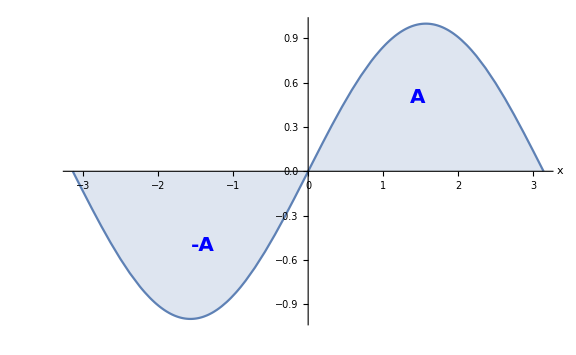

```mathematica
lText = Text[Style["-A", Blue, Bold, FontSize->20], {-Pi/2, -0.5}, align[Left]];
rText = Text[Style["A", Blue, Bold, FontSize->20], {Pi/2, 0.5}, align[Right]];
txt = Graphics[{lText, rText}];
Show[Plot[Sin[x], {x, -π, π}, Filling->Axis, ImageSize->Large, Ticks->None, AxesLabel->Automatic], txt]
```

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiDefScomp3"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodiDefScomp5"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->500, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics- -Graphics-

## Proprietà dell’intervallo di integrazione

Additività rispetto all’intervallo di integrazione: 
	
Sia f(x) una funzione definita in un intervallo [a, b] e sia a < c < b. Allora

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(x)\,dx=\\int_{a}^{c}f(x)\,dx+\\int_{c}^{b}f(x)\,dx", Magnification->3]
```

-Graphics-

Questa semplice proprietà si può vedere facilmente dai seguenti grafici

```mathematica
<<"Grafici.m";
grafico9
```

Spezzare l’intervallo di integrazione è utile per integrare il valore assoluto di una funzione, vediamone un esempio.

## Esempio

Sia f(x) = 1 - x^2. Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1} |f(x)|\,dx", Magnification->3]
```

-Graphics-

Il valore assoluto agisce sulla definizione cambiandone il segno se negativa.
La cosa da fare è quindi vedere dove la nostra f(x) è negativa.
Vediamo che lo è nell’intervallo [-4, -1] e positiva in [-1, 1] quindi cominciamo con spezzare l’intervallo in x = 1.

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1} |f(x)|\,dx=\\int_{-4}^{-1} |f(x)|\,dx+\\int_{-1}^{1} |f(x)|\,dx", Magnification->3]
```

-Graphics-

Perché spezzare l’intervallo? Dato che f(x) = 1 - x^2 in [- 1, 1] è positiva il valore assoluto diventa inutile, 
mentre nell’intervallo [-4,-1] la funzione f(x) è negativa e quindi cambia di segno, ovvero

```mathematica
<<MaTeX`
MaTeX["|f(x)|=-f(x)=-(1-x^2)=x^2-1", Magnification->3]
```

-Graphics-

L’integrale diventa quindi

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{1}|1-x^2|\,dx=\\int_{-4}^{-1}|1-x^2|\,dx+\\int_{-1}^{1}|1-x^2|\,dx=\\int_{-4}^{-1}x^2-1\,dx+\\int_{-1}^{1} 1-x^2\,dx", Magnification->3]
```

-Graphics-

Non ci resta altro da fare che integrare i due polinomi arrivando così al risultato

```mathematica
<<MaTeX`
MaTeX["\\int_{-4}^{-1}x^2-1\,dx+\\int_{-1}^{1} 1-x^2\,dx=\\left[\\left(-\\frac{1}{3}+\\frac{4^3}{3}\\right)-(-1+4)\\right]+\\left[2-\\left(\\frac{1}{3}+\\frac{1}{3}\\right)\\right]=\\frac{58}{3}", Magnification->3]
```

-Graphics-

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodo di sostituzione per i definiti!", {"Project.nb","MetodoDefSostituzione"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodo di sostituzione per i definiti!Project.nbMetodoDefSostituzioneProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodiDefScomp4"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Sostituzione - Definiti

## Prima formula di sostituzione

Come calcolare integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi(x))\\phi'(x) \,dx", Magnification->3]
```

-Graphics-

Come detto nell’introduzione, per risolvere un generico integrale definito partiamo dal cercare una primitiva della funzione integranda, andiamo a  richiamare quindi la formula per gli integrali indefiniti risolti con il primo metodo di sostituzione.
La formula adattata ai definiti è

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi(x))\\phi'(x) \,dx=\\int_{\\phi(a)}^{\\phi(b)} f(t) \,dt", Magnification->3]
```

-Graphics-

Osserviamo che al momento della sostituzione t = ϕ(x), cambiano anche gli estremi di integrazione! Vediamo meglio come funziona il metodo 
con un esempio.

## Esempio

Calcolare

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{e} \\frac{\\ln(x)}{x}\,dx", Magnification->3]
```

-Graphics-

Determiniamo la funzione da sostituire, cioè

```mathematica
<<MaTeX`
MaTeX["\\phi(x)=\\ln(x) \\quad \\Longrightarrow \\quad dt=\\phi'(x) dx=\\frac{1}{x} dx", Magnification->3]
```

-Graphics-

Calcoliamo i nuovi estremi di integrazione:

```mathematica
<<MaTeX`
MaTeX["\\phi(1)=\\ln(1)=0", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\phi(e)=\\ln(e)=1", Magnification->3]
```

-Graphics-

Quindi l’integrale diventa immediato

```mathematica
<<MaTeX`
MaTeX["\\int_{\\phi(a)}^{\\phi(b)} f(t) \,dt=\\int_{0}^{1} t \,dt=\\frac{1}{2}", Magnification->3]
```

-Graphics-

```mathematica
Framed[Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];]
Button[ImageRotate[-Graphics-] ,ButtonData->NotebookLocate["MetodoDefSostituzione2"]; ],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Seconda formula di sostituzione

Andiamo a vedere come risolvere integrali del tipo

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi (x)) \, dx", Magnification->3]
```

-Graphics-

Per l’analogia della formula rimandiamo alla teoria degli integrali indefiniti risolti con il secondo metodo di sostituzione. 
Come fatto in precedenza dobbiamo quindi modificare, in base alla sostituzione fatta, gli estremi di integrzione, la formula adattata ai definiti sarà

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} f(\\phi (x)) \, dx=\\int_{\\phi(a)}^{\\phi(b)} f(t)\\psi'(t) \,dt", Magnification->3]
```

-Graphics-

Vediamola all’azione con un esempio:

## Esempio 1

Calcolare l’area sottostante alla curva di funzione f(x) = 1/(1 + √x) tra 1 e 4 
La soluzione del problema equivale quindi a calcolare il seguente integrale definito

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4} \\frac{1}{1+\\sqrt{x}} \,dx", Magnification->3]
```

-Graphics-

Sembra proprio un integrale da risolvere con il secondo metodo di sostituzione!
Andiamo a sostituire t = ϕ(x) = √x, questa ha inversa x = t^2 e quindi possiamo applicare la formula di sostituzione, vediamo come cambiano il dx e 
gli estremi di integrazione

```mathematica
<<MaTeX`
MaTeX["x=\\psi(t)=t^2 \\quad \\Longrightarrow \\quad dx=\\psi'(t)dt=2tdt", Magnification->3]
```

-Graphics-

```mathematica
<<MaTeX`
MaTeX["\\phi(1)=\\sqrt{1}=1 \\quad, \\quad \\phi(4)=\\sqrt{4}=2", Magnification->3]
```

-Graphics-

Quindi l’integrale nella nuova variabile diventa

```mathematica
<<MaTeX`
MaTeX["\\int_{1}^{4} \\frac{1}{1+\\sqrt{x}} \,dx= \\int_{\\phi(1)=1}^{\\phi(4)=2} \\frac{1}{1+t}\\underbrace{2t \,dt}_{dx} =2\\int_{1}^{2} \\frac{t}{t+1}\,dt", Magnification->3]
```

-Graphics-

Ora vediamo che la funzione da integrare sembra abbastanza semplice, ma non rientra negli integrali fondamentali ... senza utilizzare un altro metodo 
di integrazione e perderci in altri conti infiniti possiamo proseguire l’integrazione con un trucco molto comune in matematica: andiamo a sommare 
e sottrarre un 1 al numeratore dell’integranda e vediamo che succede

```mathematica
<<MaTeX`
MaTeX["2\\int_{1}^{2} \\frac{t}{t+1}\,dt=2\\int_{1}^{2} \\frac{t+1-1}{t+1}\,dt=2\\left( \\int_{1}^{2} \\frac{t+1}{t+1}\,dt+\\int_{1}^{2} \\frac{-1}{t+1}\,dt \\right)=2 \\int_{1}^{2} 1\,dt-2\\int_{1}^{2} \\frac{1}{t+1}\,dt", Magnification->3]
```

-Graphics-

Ora ci siamo ricondotti a due integrali che conosciamo bene! Quindi

```mathematica
<<MaTeX`
MaTeX["2(2-1)-2( \\ln(2+1)-\\ln(1+1))=2+2\\ln(2)-2\\ln(3)", Magnification->3]
```

-Graphics-

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Definiti Risoluzione per Sostituzione","https://www.youtube.com/watch?v=asTbOZk9OF4&index=4&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Definiti Risoluzione per Sostituzione](https://www.youtube.com/watch?v=asTbOZk9OF4&index=4&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Metodo per parti dei definiti!", {"Project.nb","MetodiDefParti"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Metodo per parti dei definiti!Project.nbMetodiDefPartiProject.nb

```mathematica
Framed[Button[ ImageRotate[-Graphics-],ButtonData->NotebookLocate["MetodoDefSostituzione"];] 
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->400, Alignment->Baseline]
```

-Graphics- -Graphics- -Graphics-

## Per Parti - Definiti

Come calcolare l’integrale definito di un prodotto di funzioni?

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} h(x)g(x) \,dx", Magnification->3]
```

-Graphics-

Rimandiamo alla sezione metodo di integrazione per parti degli integrali indefiniti per analogia della formula
La formula adattata ai definiti è la seguente

```mathematica
<<MaTeX`
MaTeX["\\int_{a}^{b} g'(x)f(x)\,dx=g(b)f(b)-g(a)f(a)-\\int_{a}^{b} g(x)f'(x) \,dx", Magnification->3]
```

-Graphics-

Vediamola subito con un esempio

## Esempio

Trovare l’area sotto la curva di funzione f(x) = xe^x tra 0 e 1 e cioe' dobbiamo risolvere il seguente integrale definito

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1} xe^x \,dx", Magnification->3]
```

-Graphics-

Applichiamo la formula di integrazione per parti

```mathematica
<<MaTeX`
MaTeX["\\int_{0}^{1}\\underbrace{x}_{f}\\underbrace{e^x}_{g'}\,dx= e - \\int_{0}^{1} 1\\cdot e^x \,dx= e -\\int_{0}^{1} e^x \,dx", Magnification->3]
```

-Graphics-

e quindi

```mathematica
<<MaTeX`
MaTeX["e -\\int_{0}^{1} e^x \,dx= e-(e-1)=1", Magnification->3]
```

-Graphics-

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Definiti Risoluzione per Parti","https://www.youtube.com/watch?v=-SiZBhS3Iiw&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51&index=6"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Definiti Risoluzione per Parti](https://www.youtube.com/watch?v=-SiZBhS3Iiw&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51&index=6)

```mathematica
"Passa alla prossima sezione: "Framed[Hyperlink["Funzioni razionali dei definiti!", {"Project.nb","MetodiDefRazionali"}],
FrameStyle->Directive[Orange,12], Background->LightBlue]
```

Passa alla prossima sezione:  Funzioni razionali dei definiti!Project.nbMetodiDefRazionaliProject.nb

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-

## Funzioni Razionali - Definiti

Per calcolare l’integrale definito di una funzione razionale non facciamo altro che trovare una primitiva della funzione stessa, quindi rimandiamo alla parte degli integrali indefiniti in cui spieghiamo come trovarla. 
Facciamo comunque un semplice esempio:

## Esempio

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{x^2+x-2} \,dx", Magnification->3]
```

-Graphics-

Possiamo scomporre il denominatore, cioe siamo nel caso 3 della teoria di integrazione di funzioni razionali.

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{x^2+x-2} \,dx = \\int_{2}^{5} \\frac{2x+3}{(x+2)(x-1)} \,dx", Magnification->3]
```

-Graphics-

dobbiamo quindi trovare i fratti semplici da integrare

```mathematica
<<MaTeX`
MaTeX["\\frac{2x+3}{(x+2)(x-1)}=\\frac{A}{(x+2)}+\\frac{B}{(x-1)}= \\frac{A(x-1)+B(x+2)}{(x+2)(x-1)}=\\frac{(A+B)x+(2B-A)}{(x+2)(x-1)}", Magnification->3]
```

-Graphics-

impostiamo il sistema lineare { A + B = 2, 2B - A = 3}

troviamo A = 1/3 e B = 5/3, perciò

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{(x+2)(x-1)} \,dx=\\frac{1}{3}\\int_{2}^{5}\\frac{1}{(x+2)}\,dx +\\frac{5}{3}\\int_{2}^{5}\\frac{1}{(x-1)}\,dx", Magnification->3]
```

-Graphics-

sono entrambi integrali fondamentali, usando quindi il teorema fondamentale

```mathematica
<<MaTeX`
MaTeX["\\frac{1}{3}\\left[\\ln|5+2|-\\ln|2+2|\\right]+\\frac{5}{3}\\left[\\ln|5-1|-\\ln|2-1|\\right]=\\frac{1}{3}\\left[\\ln(7)-\\ln(4)+5\\ln(4)-5\\ln(1)\\right]=\\frac{1}{3}\\left[\\ln(7)+4\\ln(4)\\right]", Magnification->3]
```

-Graphics-

In conclusione

```mathematica
<<MaTeX`
MaTeX["\\int_{2}^{5} \\frac{2x+3}{x^2+x-2} \,dx = \\frac{1}{3}\\left[\\ln(7)+4\\ln(4)\\right]", Magnification->3]
```

-Graphics-

```mathematica
Framed[Hyperlink["Segui il professor Tommaso in: Integrali Definiti Risoluzione dei Razionali","https://www.youtube.com/watch?v=jjg5AWPetYY&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51"],
FrameStyle->Directive[Orange,12], Background->LightBlue, BaseStyle->{24, Bold}]
```

[Segui il professor Tommaso in: Integrali Definiti Risoluzione dei Razionali](https://www.youtube.com/watch?v=jjg5AWPetYY&list=PLL5JL8XENJdK5okbE_GA4RJLKpadJXn51)

```mathematica
Framed[
Button[ -Graphics-,ButtonData->NotebookLocate["Metodi"];] 
Button[-Graphics-, ButtonData->NotebookLocate["Index"];],
 FrameStyle->Directive[Orange, 52], RoundingRadius->50, ImageSize->300, Alignment->Baseline]
```

-Graphics- -Graphics-